# Singlet B + Φ Benchmarks for Collider searches

## Initialisations

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
mt=173.2;
mb=4.2;
mW=80.385;
mZ=91.1876;
mh=125;
αEM=1/127.9;
αS=0.1184;
e=Sqrt[4 π αEM];
sw2=0.2312;
sw=Sqrt[sw2];
cw=Sqrt[1-sw2];
tw=sw/cw;
gW=e/sw;
gZ=gW/cw;
v=2 mW sw/e;
Nc=3;
Qt=2/3;
Qb=-1/3;
```

Mixing Angles

```mathematica
tan2θL[m11_,m12_,m21_,m22_]:=-2(m11 m21+m22 m12)/((m11^2+m12^2)-(m22^2+m21^2))
tan2θR[m11_,m12_,m21_,m22_]:=-2(m11 m12+m22 m21)/((m11^2+m21^2)-(m22^2+m12^2))
sθL[m11_,m12_,m21_,m22_]:=Sin[ArcTan[tan2θL[m11,m12,m21,m22]]/2]
sθR[m11_,m12_,m21_,m22_]:=Sin[ArcTan[tan2θR[m11,m12,m21,m22]]/2]
cθL[m11_,m12_,m21_,m22_]:=Cos[ArcTan[tan2θL[m11,m12,m21,m22]]/2]
cθR[m11_,m12_,m21_,m22_]:=Cos[ArcTan[tan2θR[m11,m12,m21,m22]]/2]
```

Mass Eigenvalues

```mathematica
mq1[m11_,m12_,m21_,m22_]:=(1/Sqrt[2])Sqrt[(m11^2+m12^2+m21^2+m22^2)-Sqrt[(m11^2+m12^2+m21^2+m22^2)^2-4(m11 m22-m12 m21)^2]]
mq2[m11_,m12_,m21_,m22_]:=(1/Sqrt[2])Sqrt[(m11^2+m12^2+m21^2+m22^2)+Sqrt[(m11^2+m12^2+m21^2+m22^2)^2-4(m11 m22-m12 m21)^2]]
```

Mass Ratios

```mathematica
xqt[m11_,m12_,m21_,m22_]:=mt/mq2[m11,m12,m21,m22]
xqb[m11_,m12_,m21_,m22_]:=mb/mq2[m11,m12,m21,m22]
xqW[m11_,m12_,m21_,m22_]:=mW/mq2[m11,m12,m21,m22]
xqZ[m11_,m12_,m21_,m22_]:=mZ/mq2[m11,m12,m21,m22]
xqh[m11_,m12_,m21_,m22_]:=mh/mq2[m11,m12,m21,m22]
xqϕ[mϕ_,m11_,m12_,m21_,m22_]:=mϕ/mq2[m11,m12,m21,m22]
```

Phase Space Function

```mathematica
λ[x_,y_]:=1+x^2+y^2-2 x-2 y-2 x y
```

Loop Functions

```mathematica
ηp[τ_]:=1+Sqrt[1-τ]
ηm[τ_]:=1-Sqrt[1-τ]
f[τ_]:=HeavisideTheta[τ-1](ArcSin[1/Sqrt[τ]])^2-HeavisideTheta[1-τ](1/4)(Log[ηp[τ]/ηm[τ]]-I π)^2
f12ϕ[τ_]:=-2τ(1+(1-τ) f[τ])
f12η[τ_]:=-2τ f[τ]
g[τ_]:=HeavisideTheta[τ-1](Sqrt[τ-1])(ArcSin[1/Sqrt[τ]]) +
HeavisideTheta[1-τ] (Sqrt[1-τ]/2)(Log[(1+Sqrt[1-τ])/(1-Sqrt[1 - τ]) - I π])
Iphi[τ_,λ_] := ((τ λ)/(2(τ-λ))) + (((τ^2 λ^2+τ λ(τ - λ))/(2(τ-λ)^2))(f[τ]-f[λ]))+ ((τ^2 λ)/(τ - λ)^2)(g[τ]-g[λ])
IEta[τ_,λ_]:= ((τ λ)/(2 (τ-λ)))(f[τ]-f[λ])
```

#### Limits from γγ data

```mathematica
MXCSobs=Import["exclusion_data/MS_CS_ATLAS_observed_2102-13405.dat",{"Data",{All},{1,2}}];
FFMXCSobs=Interpolation[MXCSobs];
MXCE=Import["exclusion_data/A_ggF_139.dat",{"Data",{All},{1,2}}];
FFMXCE=Interpolation[MXCE];
Mησ=Import["exclusion_data/meta_CS_gg2eta_k0_01.dat",{"Data",{All},{1,2}}];
FFMησ=Interpolation[Mησ];
Mϕσ=Import["exclusion_data/mphi_CS_gg2phi_k0_01.dat",{"Data",{All},{1,2}}];
FFMϕσ=Interpolation[Mϕσ];
σηLO=Import["exclusion_data/mass_cs_eta.dat",{"Data",{All},{1,2}}];
FFσηLO=Interpolation[σηLO];
σηNNLO=Import["exclusion_data/mass_cs_eta.dat",{"Data",{All},{1,4}}];
FFσηNNLO=Interpolation[σηNNLO];
σϕLO=Import["exclusion_data/mass_cs_phi.dat",{"Data",{All},{1,2}}];
FFσϕLO=Interpolation[σϕLO];
σϕNNLO=Import["exclusion_data/mass_cs_phi.dat",{"Data",{All},{1,4}}];
FFσϕNNLO=Interpolation[σϕNNLO];
Remove[MXCSobs];
Remove[MXCE];
Remove[Mησ];
Remove[Mϕσ];
Remove[σηLO];
Remove[σηNNLO];
Remove[σϕLO];
Remove[σϕNNLO];
```

Limits from B’ LHC searches

```mathematica
BpSD=Import["exclusion_data/bPhi_lims_singlet.txt",{"Data",{All},{2,1}}];
FBpSDlim=Interpolation[BpSD];
Remove[BpSD];
```

## Singlet B - Model Information

## b_2 Decay

#### b_2 -> tW

```mathematica
kb2LtLW[m11_,m12_,m21_,m22_]:=gW sθL[m11,m12,m21,m22]/Sqrt[2]
kb2RtRW[m11_,m12_,m21_,m22_]:=0
Γb2tW[m11_,m12_,m21_,m22_]:=Which[mq2[m11,m12,m21,m22]>mt+mW,(1/(32 π)) (mq2[m11,m12,m21,m22]^3/mW^2) ((kb2LtLW[m11,m12,m21,m22]^2+kb2RtRW[m11,m12,m21,m22]^2) ((1-xqt[m11,m12,m21,m22]^2)^2+xqW[m11,m12,m21,m22]^2(1+xqt[m11,m12,m21,m22]^2)-2 xqW[m11,m12,m21,m22]^4)-12 kb2LtLW[m11,m12,m21,m22] kb2RtRW[m11,m12,m21,m22] xqt[m11,m12,m21,m22] xqW[m11,m12,m21,m22]^2) Sqrt[λ[xqt[m11,m12,m21,m22]^2,xqW[m11,m12,m21,m22]^2]],mq2[m11,m12,m21,m22]<mt+mW,0]
```

#### b_2 -> bZ

```mathematica
kb2Lb1LZ[m11_,m12_,m21_,m22_]:=-(gZ/2) cθL[m11,m12,m21,m22] sθL[m11,m12,m21,m22]
kb2Rb1RZ[m11_,m12_,m21_,m22_]:=0
Γb2bZ[m11_,m12_,m21_,m22_]:=Which[mq2[m11,m12,m21,m22]>mq1[m11,m12,m21,m22]+mZ,(1/(32 π)) (mq2[m11,m12,m21,m22]^3/mZ^2) ((kb2Lb1LZ[m11,m12,m21,m22]^2+kb2Rb1RZ[m11,m12,m21,m22]^2) ((1-xqb[m11,m12,m21,m22]^2)^2+xqZ[m11,m12,m21,m22]^2 (1+xqb[m11,m12,m21,m22]^2)-2 xqZ[m11,m12,m21,m22]^4)-12 kb2Lb1LZ[m11,m12,m21,m22] kb2Rb1RZ[m11,m12,m21,m22] xqb[m11,m12,m21,m22] xqZ[m11,m12,m21,m22]^2) Sqrt[λ[xqb[m11,m12,m21,m22]^2,xqZ[m11,m12,m21,m22]^2]],mq2[m11,m12,m21,m22]<mq1[m11,m12,m21,m22]+mZ,0]
```

#### b_2 -> bH

```mathematica
kb1Lb2Rh[m11_,m12_,m21_,m22_]:=(m11 cθL[m11,m12,m21,m22] sθR[m11,m12,m21,m22]+m12 cθL[m11,m12,m21,m22] cθR[m11,m12,m21,m22])/v
kb1Rb2Lh[m11_,m12_,m21_,m22_]:=(m11 sθL[m11,m12,m21,m22] cθR[m11,m12,m21,m22]-m12 sθL[m11,m12,m21,m22] sθR[m11,m12,m21,m22])/v
Γb2bh[m11_,m12_,m21_,m22_]:=Which[mq2[m11,m12,m21,m22]>mq1[m11,m12,m21,m22]+mh,(1/(32 π)) mq2[m11,m12,m21,m22] ((kb1Lb2Rh[m11,m12,m21,m22]^2+kb1Rb2Lh[m11,m12,m21,m22]^2) (1+xqb[m11,m12,m21,m22]^2-xqh[m11,m12,m21,m22]^2)+4 kb1Lb2Rh[m11,m12,m21,m22]kb1Rb2Lh[m11,m12,m21,m22] xqb[m11,m12,m21,m22]) Sqrt[λ[xqb[m11,m12,m21,m22]^2,xqh[m11,m12,m21,m22]^2]],mq2[m11,m12,m21,m22]<mq1[m11,m12,m21,m22]+mh,0]
```

#### b_2 -> bΦ

```mathematica
kb1Lb2Rϕ[m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=-λaϕ sθL[m11,m12,m21,m22] cθR[m11,m12,m21,m22]-λbϕ sθL[m11,m12,m21,m22] sθR[m11,m12,m21,m22]
kb1Rb2Lϕ[m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=-λaϕ cθL[m11,m12,m21,m22] sθR[m11,m12,m21,m22]+λbϕ cθL[m11,m12,m21,m22] cθR[m11,m12,m21,m22]
Γb2bϕ[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=Which[mq2[m11,m12,m21,m22]>mq1[m11,m12,m21,m22]+mϕ,(1/(32 π)) mq2[m11,m12,m21,m22] ((kb1Lb2Rϕ[m11,m12,m21,m22,λaϕ,λbϕ]^2+kb1Rb2Lϕ[m11,m12,m21,m22,λaϕ,λbϕ]^2) (1+xqb[m11,m12,m21,m22]^2-xqϕ[mϕ,m11,m12,m21,m22]^2)+4 kb1Lb2Rϕ[m11,m12,m21,m22,λaϕ,λbϕ]kb1Rb2Lϕ[m11,m12,m21,m22,λaϕ,λbϕ] xqb[m11,m12,m21,m22]) Sqrt[λ[xqb[m11,m12,m21,m22]^2,xqϕ[mϕ,m11,m12,m21,m22]^2]],mq2[m11,m12,m21,m22]<mq1[m11,m12,m21,m22]+mϕ,0]
```

#### Total Width

```mathematica
Γb2[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=Γb2tW[m11,m12,m21,m22]+Γb2bZ[m11,m12,m21,m22]+Γb2bh[m11,m12,m21,m22]+Γb2bϕ[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]
```

#### Branching Ratios

```mathematica
BRb2tW[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=Γb2tW[m11,m12,m21,m22]/Γb2[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]
BRb2bZ[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=Γb2bZ[m11,m12,m21,m22]/Γb2[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]
BRb2bh[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=Γb2bh[m11,m12,m21,m22]/Γb2[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]
BRb2bϕ[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=Γb2bϕ[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]/Γb2[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]
```

## Φ Decay

#### Loop productions

```mathematica
kb1Lb1Rϕ[m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=λaϕ sθL[m11,m12,m21,m22] sθR[m11,m12,m21,m22]-λbϕ sθL[m11,m12,m21,m22] cθR[m11,m12,m21,m22]
kb2Lb2Rϕ[m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=λaϕ cθL[m11,m12,m21,m22] cθR[m11,m12,m21,m22]+λbϕ cθL[m11,m12,m21,m22] sθR[m11,m12,m21,m22]
```

#### Φ -> γγ

```mathematica
Γϕγγb[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=(αEM^2/(256 π^3)) (mϕ^3/(mq2[m11,m12,m21,m22])^2)Nc^2(Qb)^4 (Abs[kb1Lb1Rϕ[m11,m12,m21,m22,λaϕ,λbϕ] f12ϕ[4(mq1[m11,m12,m21,m22])^2/mϕ^2]+kb2Lb2Rϕ[m11,m12,m21,m22,λaϕ,λbϕ] f12ϕ[4(mq2[m11,m12,m21,m22])^2/mϕ^2]])^2
```

#### Φ -> gg

```mathematica
Γϕggb[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=(αS^2/(128 π^3)) (mϕ^3)(Abs[kb1Lb1Rϕ[m11,m12,m21,m22,λaϕ,λbϕ] f12ϕ[4(mq1[m11,m12,m21,m22])^2/mϕ^2]/mq1[m11,m12,m21,m22]+kb2Lb2Rϕ[m11,m12,m21,m22,λaϕ,λbϕ] f12ϕ[4 mq2[m11,m12,m21,m22]^2/mϕ^2]/mq2[m11,m12,m21,m22]])^2
```

#### Φ -> bb

```mathematica
Γϕbb[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=Which[mϕ>2mq1[m11,m12,m21,m22],(3/(8π))(kb1Lb1Rϕ[m11,m12,m21,m22,λaϕ,λbϕ])^2 mϕ(1-4(mq1[m11,m12,m21,m22])^2/mϕ^2)^(3/2),mϕ<2mq1[m11,m12,m21,m22],0]
```

#### Φ -> Zγ

```mathematica
ΓϕZγb[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:= ((αEM^2 mϕ^3 Nc^2 Qb^2)/(32 π^3 sw2 cw^2))(1 - mZ^2/mϕ^2)^3(Abs[1/mq1[m11,m12,m21,m22] kb1Lb1Rϕ[m11,m12,m21,m22,λaϕ,λbϕ] (-0.5 (cθL[m11,m12,m21,m22])^2- 2 Qb sw2)  Iphi[(4(mq1[m11,m12,m21,m22])^2)/mϕ^2,(4(mq1[m11,m12,m21,m22])^2)/mZ^2]+ 1/mq2[m11,m12,m21,m22] kb2Lb2Rϕ[m11,m12,m21,m22,λaϕ,λbϕ](-0.5 (sθL[m11,m12,m21,m22])^2- 2 Qb sw2 )Iphi[(4(mq2[m11,m12,m21,m22])^2)/mϕ^2,(4(mq2[m11,m12,m21,m22])^2)/mZ^2] ])^2
```

#### Total Width

```mathematica
Γϕb[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=Γϕggb[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]+Γϕγγb[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]+Γϕbb[mϕ,m11,m12,m21,m22,λaϕ,λbϕ] + ΓϕZγb[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]
```

#### Branching Ratios

```mathematica
BRϕγγb[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=Γϕγγb[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]/Γϕb[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]
BRϕggb[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=Γϕggb[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]/Γϕb[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]
BRϕbb[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=Γϕbb[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]/Γϕb[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]
BRϕZγb[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:= ΓϕZγb[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]/Γϕb[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]
```

## Benchmark Plots

```mathematica
mϕ =400;
mb11 =mb;
mb12 = 3.660069;
mb21=0;
mb22=1200;
λaϕ=0.848120;
λbϕ=0.100024;
```

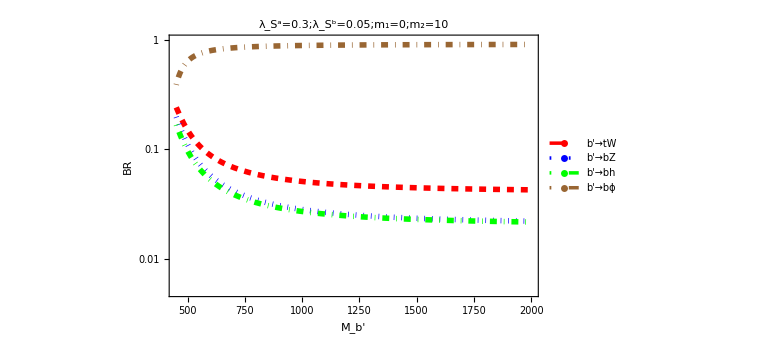

```mathematica
LogPlot[{BRb2tW[mϕ,mb11,mb12,mb21,m22,λaϕ,λbϕ],BRb2bZ[mϕ,mb11,mb12,mb21,m22,λaϕ,λbϕ],BRb2bh[mϕ,mb11,mb12,mb21,m22,λaϕ,λbϕ],BRb2bϕ[mϕ,mb11,mb12,mb21,m22,λaϕ,λbϕ]},{m22,450,2000},Frame->True,FrameStyle->Thick,PlotRange->{{450,2000},{0.005,1.001}},PlotStyle->{{Red,Dashed,Thickness[0.007]},{Blue,Dotted,Thickness[0.007]},{Green,DotDashed,Thickness[0.007]},{Brown,DotDashed,Thickness[0.007]}},PlotLabel->Style[HoldForm[ Subscript[λ, S]^a=0.3; Subscript[λ, S]^b=0.05; Subscript[m, 1]=0; Subscript[m, 2]=10],18],PlotLegends->Placed[LineLegend[Automatic,{Style["b'→tW",15],Style["b'→bZ",15],Style["b'→bh",15],Style["b'→bϕ",15]},LegendMarkers->Graphics[{Thickness[0.14],Line[{{-10,0},{10,0}}]}],LegendMarkerSize->20],{0.8,0.3}],FrameLabel->{"M_b'","BR"},LabelStyle->FontSize->20]
```

```mathematica
paralist90={};
n=0;
While[n<1001,AppendTo[paralist90,{N[400+n*1.6], BRb2tW[mϕ,mb11,mb12,mb21,N[400+n*1.6],λaϕ,λbϕ],BRb2bZ[mϕ,mb11,mb12,mb21,N[400+n*1.6],λaϕ,λbϕ],BRb2bh[mϕ,mb11,mb12,mb21,N[400+n*1.6],λaϕ,λbϕ],BRb2bϕ[mϕ,mb11,mb12,mb21,N[400+n*1.6],λaϕ,λbϕ]}];n++]
Export["benchmarks/B_1200_400_bPhiDom.dat",paralist90];
Remove[paralist90];
```

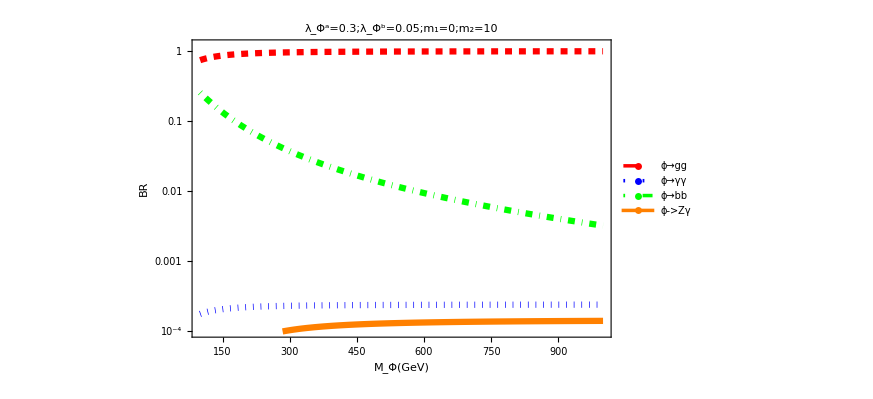

```mathematica
LogPlot[{BRϕggb[mϕ,mb11,mb12,mb21,mb22,λaϕ,λbϕ],BRϕγγb[mϕ,mb11,mb12,mb21,mb22,λaϕ,λbϕ],BRϕbb[mϕ,mb11,mb12,mb21,mb22,λaϕ,λbϕ], BRϕZγb[mϕ,mb11,mb12,mb21,mb22,λaϕ,λbϕ]},{mϕ,100,1000},Frame->True,FrameStyle->Thick,PlotRange->{{100,1000},{0.0001,1.2}},PlotLabel->Style[HoldForm[ Subscript[λ, Φ]^a=0.3; Subscript[λ, Φ]^b=0.05; Subscript[m, 1]=0; Subscript[m, 2]=10],18],PlotStyle->{{Red,Dashed,Thickness[0.007]},{Blue,Dotted,Thickness[0.007]},{Green,DotDashed,Thickness[0.007]}, {Orange,Thickness[0.007]}},PlotLegends->Placed[LineLegend[Automatic,{Style["ϕ→gg",15],Style["ϕ→γγ",15],Style["ϕ→bb",15], Style["ϕ->Zγ",15]},LegendMarkers->Graphics[{Thickness[0.14],Line[{{-10,0},{10,0}}]}],LegendMarkerSize->20],{0.9,0.8}],FrameLabel->{Subscript[M,Φ][GeV],BR},LabelStyle->FontSize->20]
```

```mathematica
paralist80={};
n=0;
While[n<1001,AppendTo[paralist80,{N[100+n*0.9], BRϕggb[N[100+n*0.9],mb11,mb12,mb21,mb22,λaϕ,λbϕ],BRϕγγb[N[100+n*0.9],mb11,mb12,mb21,mb22,λaϕ,λbϕ],BRϕbb[N[100+n*0.9],mb11,mb12,mb21,mb22,λaϕ,λbϕ],BRϕZγb[N[100+n*0.9],mb11,mb12,mb21,mb22,λaϕ,λbϕ]}];n++]
Export["benchmarks/Phi_1200_400_bPhiDom.dat",paralist80];
Remove[paralist80];
```

### Misc.

NP coupling   from [arxiv:1305.4172], eq. 2.20

```mathematica
κTL[sθL_,cθL_, sθR_,cθR_, mVLQ_] := sθL^2 + (cθL*sθL)^2*0.5 +((mt/v)*cθL*sθR + (m12/v)*cθL*cθR)^2*(0.5 - (mh/mVLQ)^2)
```

## Benchmark Scan

```mathematica
mb11 = mb;
Rλa:=RandomReal[{0.0,1.0}];
Rλb:=RandomReal[{0.0,1.0}];
m21=RandomReal[{0,50}];
Rm12:=RandomReal[{0,50}];
```

```mathematica
LLBR = 0.5;
```

#### M_b_2 , M_Φ Def.

```mathematica
mb22 = 1200;
mS = 400;
npts=70000;
```

#### BR(Φ -> gg) > 0.5

```mathematica
infoListColor = {};
Monitor[For[n=0, n < npts, n++,
{m12,λa,λb}={Rm12,Rλa,Rλb}; 
If[BRb2bϕ[mS,mb11,m12,m21,mb22,λa,λb]> FBpSDlim[mq2[mb11,m12,m21,mb22]/1000]&& ((kb1Lb1Rϕ[mb11,m12,m21,mb22,λa,λb]+kb2Lb2Rϕ[mb11,m12,m21,mb22,λa,λb])^2/0.01^2/48^2/π^4) (FFσϕNNLO[mS]/FFσϕLO[mS]) FFMϕσ[mS] FFMXCE[mS]BRϕγγb[mS,mb11,m12,m21,mb22,λa,λb]1000<FFMXCSobs[mS],If[BRϕggb[mS,mb11,m12,m21,mb22,λa,λb]>LLBR,AppendTo[infoListColor,{ m12, m21,λa, λb,BRb2bϕ[mS,mb11,m12,m21,mb22,λa,λb],BRϕggb[mS,mb11,m12,m21,mb22,λa,λb],BRϕbb[mS,mb11,m12,m21,mb22,λa,λb], Γb2[mS,mb11,m12,m21,mb22,λa,λb],Γϕb[mS,mb11,m12,m21,mb22,λa,λb]}]]]];,Row[{ProgressIndicator[n,{0,npts}],n}," "]]
Export["Scans/SingB/finalRange/PS_Phibb_"<>ToString[LLBR]<>"_mBp_"<>ToString[mb22]<>"_mPhi_"<>ToString[mS]<>"_"<>ToString[IntegerPart[npts/1000]]<>"k.dat", infoListColor];
Remove[infoListColor];
```

```mathematica
FBpSDlim[mq2[mb11,m12,m21,1000]/1000] (* Minimum Allowed Subscript[β, bΦ] for Subscript[M, Subscript[b, 2]] = 1 TeV*)
```

0.702883

```mathematica
FBpSDlim[mq2[mb11,m12,m21,1100]/1000] (* Minimum Allowed Subscript[β, bΦ] for Subscript[M, Subscript[b, 2]] = 1.1 TeV*)
```

0.567294

## BR(B → bΦ) contour scan

```mathematica
mb11 = mb;
m21=0;
```

```mathematica
Rm12:=RandomReal[{0,50}];
λa=0.1;
Rλb:=RandomReal[{0.0,1.0}];
```

```mathematica
mb22 = 1200;
mS = 300;
npts=5000;
LLBR = 0.95;
```

Parameter Scan (LHC Limits (B, ϕ) + BR(B → bϕ) > β )

```mathematica
infoListColor = {};
Monitor[For[n=0, n < npts, n++,
{m12,λb}={Rm12,Rλb}; 
If[BRb2bϕ[mS,mb11,m12,m21,mb22,λa,λb]> FBpSDlim[mq2[mb11,m12,m21,mb22]/1000]&&((kb1Lb1Rϕ[mb11,m12,m21,mb22,λa,λb]+kb2Lb2Rϕ[mb11,m12,m21,mb22,λa,λb])^2/0.01^2/48^2/π^4) (FFσϕNNLO[mS]/FFσϕLO[mS]) FFMϕσ[mS] FFMXCE[mS]BRϕγγb[mS,mb11,m12,m21,mb22,λa,λb]1000<FFMXCSobs[mS],If[BRϕggb[mS,mb11,m12,m21,mb22,λa,λb]+BRϕbb[mS,mb11,m12,m21,mb22,λa,λb]>LLBR,AppendTo[infoListColor,Map[NumberForm[#,3]&,{ m12,λa, λb,BRb2bϕ[mS,mb11,m12,m21,mb22,λa,λb]}]]]]];,Row[{ProgressIndicator[n,{0,npts}],n}," "]]
Export["Scans/SingB/BPhi_ContPlt/lamFixed/lamA"<>ToString[λa]<>"_mBp_"<>ToString[mb22]<>"_mPhi_"<>ToString[mS]<>"_"<>ToString[IntegerPart[npts/1000]]<>"k.dat", infoListColor];
Remove[infoListColor];
```

## Systematic Scan - λ_a constant

```mathematica
mb11 = mb;
m21=0;
```

```mathematica
mb22 = 1200;
mS = 300;
LLBR = 0.95;
```

```mathematica
infoListColor ={};
λa =0.1;Table[If[((kb1Lb1Rϕ[mb11,m12,m21,mb22,λa,λb]+kb2Lb2Rϕ[mb11,m12,m21,mb22,λa,λb])^2/0.01^2/48^2/π^4) (FFσϕNNLO[mS]/FFσϕLO[mS]) FFMϕσ[mS] FFMXCE[mS]BRϕγγb[mS,mb11,m12,m21,mb22,λa,λb]1000<FFMXCSobs[mS]&&BRϕggb[mS,mb11,m12,m21,mb22,λa,λb]+BRϕbb[mS,mb11,m12,m21,mb22,λa,λb]>LLBR,AppendTo[infoListColor,Map[NumberForm[#,4]&,{ λb,m12, BRb2bϕ[mS,mb11,m12,m21,mb22,λa,λb]}]]], {λb,0.01,1,0.01}, {m12,0.5,50,0.5}];
```

```mathematica
SortBy[N@* First]@infoListColor;
```

```mathematica
Export["Scans/SingB/BPhi_ContPlt/lamFixed/lamA"<>ToString[λa]<>"_mBp_"<>ToString[mb22]<>"_mPhi_"<>ToString[mS]<>".dat", infoListColor];
Remove[infoListColor];
```

## Systematic Scan - λ_b constant

```mathematica
mb11 = mb;
m21=0;
```

```mathematica
mb22 = 1200;
mS = 300;
LLBR = 0.95;
```

```mathematica
infoListColor ={};
λb =0.3;Table[If[((kb1Lb1Rϕ[mb11,m12,m21,mb22,λa,λb]+kb2Lb2Rϕ[mb11,m12,m21,mb22,λa,λb])^2/0.01^2/48^2/π^4) (FFσϕNNLO[mS]/FFσϕLO[mS]) FFMϕσ[mS] FFMXCE[mS]BRϕγγb[mS,mb11,m12,m21,mb22,λa,λb]1000<FFMXCSobs[mS]&&BRϕggb[mS,mb11,m12,m21,mb22,λa,λb]+BRϕbb[mS,mb11,m12,m21,mb22,λa,λb]>LLBR,AppendTo[infoListColor,Map[NumberForm[#,4]&,{ λa,m12, BRb2bϕ[mS,mb11,m12,m21,mb22,λa,λb]}]]], {λa,0.01,1,0.01}, {m12,0.5,50,0.5}];
```

```mathematica
SortBy[N@* First]@infoListColor;
```

```mathematica
Export["Scans/SingB/BPhi_ContPlt/lamFixed/lamB"<>ToString[λb]<>"_mBp_"<>ToString[mb22]<>"_mPhi_"<>ToString[mS]<>".dat", infoListColor];
Remove[infoListColor];
```